```mathematica
(*mub=1307.5/(1+0.288*s)
```

```mathematica
(*tc=158.4/(1+Exp[2.60-Log[s]/0.45])
```

```mathematica
(*f={mub==a/(1+b*s),tc==e/(1+Exp[c-Log[s]/d])}
```

```mathematica
(*f2=Eliminate[f,s]//FullSimplify
```

```mathematica
(*Solve[f2,tc,Reals]//Simplify
```

```mathematica
tc=e/(1+Exp[c-Log[a/(b d mub)-1/(b d)]])
```

e/(1+ⅇ^c/(-1/(b d)+a/(b d mub)))

```mathematica
Tc={167.8,164.3,159.9,159.8,157.5,150.6,143.8};
muB={27.0,69.2,104.7,151.9,195.6,292.5,399.8};
(*Tc={159.9,159.8,157.5,150.6};
muB={104.7,151.9,195.6,292.5};*)data=Transpose[{muB,Tc}]
```

{{27.,167.8},{69.2,164.3},{104.7,159.9},{151.9,159.8},{195.6,157.5},{292.5,150.6},{399.8,143.8}}

```mathematica
fitline=NonlinearModelFit[data,{e/(1+Exp[c-Log[a/(b d x)-1/(b d)]]),a>0},{a,b,c,d,e},x]
```

FittedModel[-1581.35/(1+(2.75200239406×10^1080)/(-1.61573×10^-7+(1.49929×10^-6)/x))]

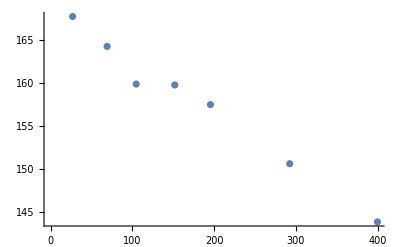

```mathematica
ListPlot[data]
```

```mathematica
Normal[fitline]
```

-1581.35/(1+(2.75200239406×10^1080)/(-1.61573×10^-7+(1.49929×10^-6)/x))

```mathematica
tc2[mub2_]:=1.0073380292036989/(1+(5.378173651528706767727039693192`12.807948922996626*^608)/(-5.090006132863423*^-7+(5.089539102763219*^-6)/mub2))
```

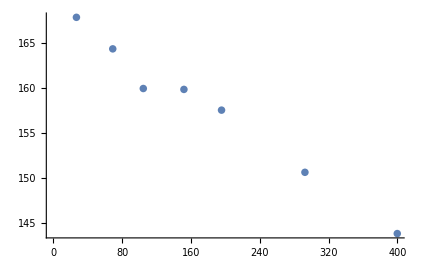

```mathematica
Show[ListPlot[data],Plot[tc2[x],{x,0,400}]]
```

```mathematica
158.4/(1+13.463738035001692/(-3.4722222222222223+4539.930555555556/x)^2.2222222222222223)
```

158.4/(1+13.4637/(-3.47222+4539.93/x)^2.22222)

```mathematica
fitts=NonlinearModelFit[data,{a/(1+b/(c+d/x)^e),150.<a<170.,1.<b<30.,-10.<c<0,2000<d<6000,0<e<10},{a,b,c,d,e},x]
```

FittedModel[170./(1+1./(-5.59245+(«18»)/x)^0.761299)]

```mathematica
Normal[fitts]
```

170./(1+1./(-5.59245+6000./x)^0.761299)

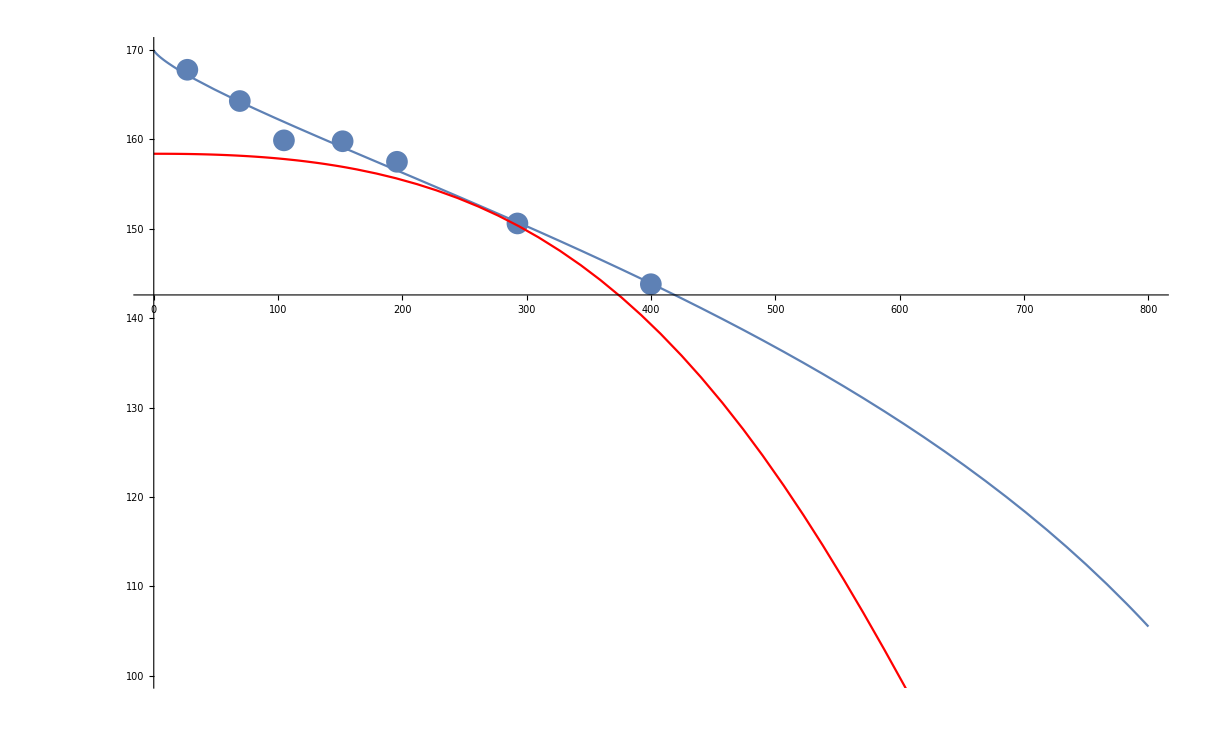

```mathematica
Show[ListPlot[data],Plot[169.9999865425475/(1+1.0000001360663666/(-5.592445163386916+5999.998908291848/s1)^0.7612987760426763),{s1,0,800}],Plot[158.4/(1+13.463738035001692/(-3.4722222222222223+4539.930555555556/s1)^2.2222222222222223),{s1,0,800},PlotStyle->Red],PlotRange->{{0,800},{100,170}}]
```

```mathematica
158.4/(1+Exp[2.6-Log[s]/0.45])
```

158.4/(1+13.4637/s^2.22222)

```mathematica
1307.5/(1+0.288 s)
```

1307.5/(1+0.288 s)

```mathematica
(*Tc={167.8,164.3,159.9,159.8,157.5,150.6,143.8};
muB={27.0,69.2,104.7,151.9,195.6,292.5,399.8};
sNN={200.,62.4,39.0,27.0,19.6,11.5,7.7};
```

```mathematica
Tc={164.3,159.9,159.8,157.5,150.6,143.8};
muB={69.2,104.7,151.9,195.6,292.5,399.8};
sNN={62.4,39.0,27.0,19.6,11.5,7.7};
```

```mathematica
datatc=Transpose[{sNN,Tc}]
datamub=Transpose[{sNN,muB}]
```

{{62.4,164.3},{39.,159.9},{27.,159.8},{19.6,157.5},{11.5,150.6},{7.7,143.8}}

{{62.4,69.2},{39.,104.7},{27.,151.9},{19.6,195.6},{11.5,292.5},{7.7,399.8}}

```mathematica
fittsNN=Normal[fittsN=NonlinearModelFit[datatc,{a/(1+b/s^c),140<a<170,0<b<50,0<c<10},{a,b,c},s]]
fitmubsNN=Normal[fitmubsN=NonlinearModelFit[datamub,{a/(1+b s),1000<a<2000,0<b<5},{a,b},s]]
```

166.505/(1+1.24361/s^1.01236)

1221.74/(1+0.269405 s)

```mathematica
169.47479446203963/(1+0.9129755815381264/s^0.8074948720100684)/.s->7.7
```

144.155

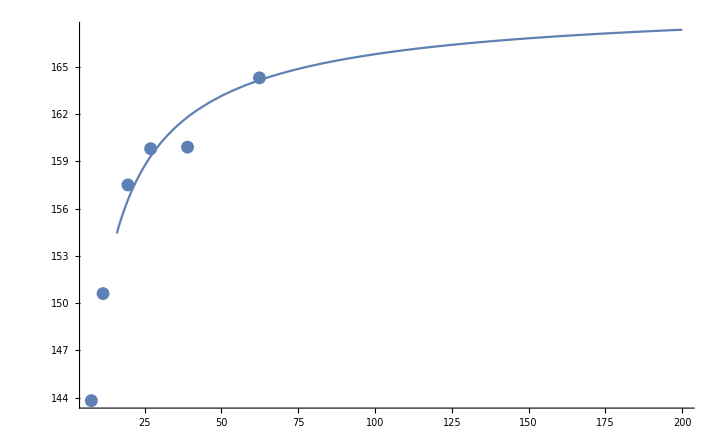

```mathematica
Show[ListPlot[datatc],Plot[166.50541085269373/(1+1.2436067390259087/s^1.0123588240888122),{s,7,200}],PlotRange->Automatic]
```

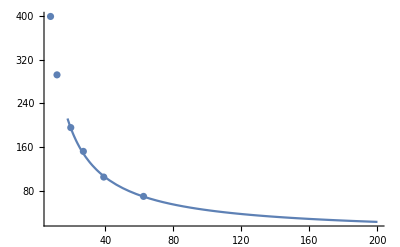

```mathematica
Show[ListPlot[datamub],Plot[1221.7421105137298/(1+0.26940455851629286 s),{s,7,200}],PlotRange->Automatic]
```

```mathematica
Tf2=169.475/(1+0.913/(1210.96/(0.266mub2)-1/0.266)^0.807)
```

169.475/(1+0.913/(-3.7594+4552.48/mub2)^0.807)

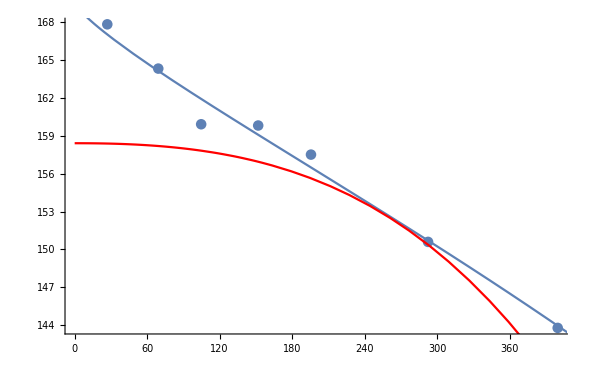

```mathematica
Show[ListPlot[data],Plot[169.475/(1+0.913/(1210.96/(0.266mub2)-1/0.266)^0.807),{mub2,0,800}],Plot[158.4/(1+13.463738035001692/(-3.4722222222222223+4539.930555555556/s1)^2.2222222222222223),{s1,0,800},PlotStyle->Red]]
```

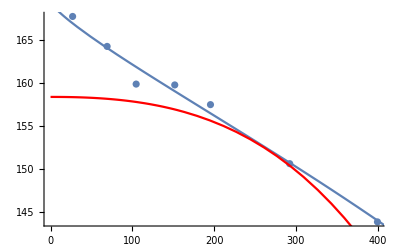

```mathematica
Show[ListPlot[data],Plot[169.475/(1+0.913/(1210.96/(0.266mub2)-1/0.266)^0.807),{mub2,0,800}],Plot[158.4/(1+13.463738035001692/(-3.4722222222222223+4539.930555555556/s1)^2.2222222222222223),{s1,0,800},PlotStyle->Red]]
```